```mathematica
MyAdjacencyMatrix[G0_]:=Module[{g=G0},n=Length[VertexList[g]];A=ConstantArray[0,{n,n}];
For[x=1,x≤n,x++,V=VertexList[NeighborhoodGraph[g,x,1]];For[y=1,y≤Length[V],y++,A[[x,V[[y]]]]=1]];
A-IdentityMatrix[n]
]
```

```mathematica
Smash[G0_,S0_]:=Module[{G=G0,S=S0,V,A,Sbar},
A=[G];V=VertexList[G];Sbar = Complement[V,S];
A[[S,S]]-A[[S,Sbar]].Inverse[A[[Sbar,Sbar]]-L*IdentityMatrix[Length[Sbar]]].A[[Sbar,S]]
]
```

```mathematica
Smash[G0_,S0_]:=Module[{G=G0,S=S0,V,A,Sbar},
(*Get the adjacency matrix of the graph*)
A=AdjacencyMatrix[G];
V=VertexList[G];
(*Map vertex labels to matrix indices*)
S=Flatten[Position[V,#]&/@S0];
Sbar=Complement[Range[Length[V]],S];
(*Compute the Schur complement formula*)
A[[S,S]]-A[[S,Sbar]].Inverse[A[[Sbar,Sbar]]-L IdentityMatrix[Length[Sbar]]].A[[Sbar,S]]
]

SmashEigen[G0_,S0_]:=Module[{G=G0,S=S0},
Eigenvalues[Smash[G,S]]
]
```

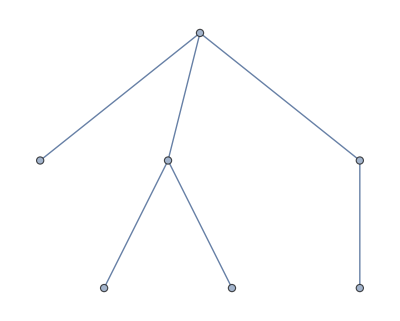

```mathematica
T=Graph[{1<->2,2<->3,3<->4,3<->5,2<->6,6<->7}]
```

```mathematica
A=AdjacencyMatrix[T]
```

SparseArray[…]

```mathematica
Eigenvalues[A]//N
```

{-2.05288,2.05288,-1.20864,1.20864,-0.569973,0.569973,0.}

```mathematica
CharacteristicPolynomial[A,z]
```

2 z-8 z^3+6 z^5-z^7

```mathematica
Factor[2 z-8 z^3+6 z^5-z^7]
```

-z (-2+8 z^2-6 z^4+z^6)

```mathematica
Factor[1+z-15 z^2+17 z^3+5 z^4-15 z^5+7 z^6-z^7]
```

-((-1+z) (1+2 z-13 z^2+4 z^3+9 z^4-6 z^5+z^6))

```mathematica
R=Simplify[Smash[T,{1,2,3}]]
```

Smash[-Graphics-,{1,2,3}]

```mathematica
B=R//.{L->1.20864}
```

Smash[-Graphics-,{1,2,3}]

```mathematica
CharacteristicPolynomial[B,z]
```

-1.65475-2.34018 z+4.27761 z^2-z^3

```mathematica
Factor[-1.654752449033625-2.3401774714539956 z+4.277608498582703 z^2-z^3]
```

-1. (-3.46418+1. z) (-1.20864+1. z) (0.395216+1. z)

```mathematica
Eigenvalues[%]
```

{3.46418,1.20864,-0.395216}

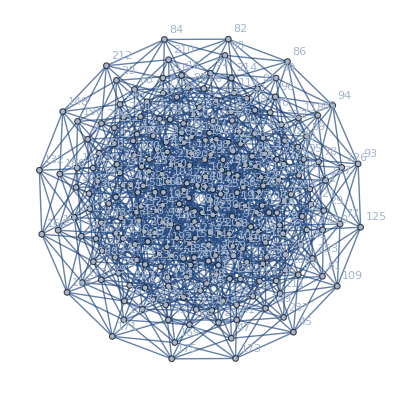

```mathematica
G=HypercubeGraph[8,VertexLabels->"Name"]
```

```mathematica
Smash[G,{1,256}]
```

Smash[-Graphics-,{1,256}]

```mathematica
Simplify[%]
```

{{(8 (-5040+1856 L^2-90 L^4+L^6))/(L (-17920+2864 L^2-104 L^4+L^6)),40320/(L (-17920+2864 L^2-104 L^4+L^6))},{40320/(L (-17920+2864 L^2-104 L^4+L^6)),(8 (-5040+1856 L^2-90 L^4+L^6))/(L (-17920+2864 L^2-104 L^4+L^6))}}

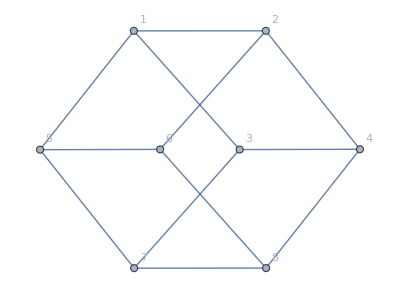

{{(2 L)/(1-3 L^2+L^4)-(L-L^3)/(1-3 L^2+L^4)-(2 L-L^3)/(1-3 L^2+L^4),1+1/(1-3 L^2+L^4)-(1-L^2)/(1-3 L^2+L^4),L/(1-3 L^2+L^4)-(2 L-L^3)/(1-3 L^2+L^4),1/(1-3 L^2+L^4)+L^2/(1-3 L^2+L^4)-(2 (1-L^2))/(1-3 L^2+L^4)},{1+1/(1-3 L^2+L^4)-(1-L^2)/(1-3 L^2+L^4),-(2 L-L^3)/(1-3 L^2+L^4),1+1/(1-3 L^2+L^4),L/(1-3 L^2+L^4)-(2 L-L^3)/(1-3 L^2+L^4)},{L/(1-3 L^2+L^4)-(2 L-L^3)/(1-3 L^2+L^4),1+1/(1-3 L^2+L^4),-(2 L-L^3)/(1-3 L^2+L^4),1+1/(1-3 L^2+L^4)-(1-L^2)/(1-3 L^2+L^4)},{1/(1-3 L^2+L^4)+L^2/(1-3 L^2+L^4)-(2 (1-L^2))/(1-3 L^2+L^4),L/(1-3 L^2+L^4)-(2 L-L^3)/(1-3 L^2+L^4),1+1/(1-3 L^2+L^4)-(1-L^2)/(1-3 L^2+L^4),(2 L)/(1-3 L^2+L^4)-(L-L^3)/(1-3 L^2+L^4)-(2 L-L^3)/(1-3 L^2+L^4)}}

```mathematica
G=HypercubeGraph[3,VertexLabels->"Name"]
Smash[G,{1,2,4,8}]
```

```mathematica
mat = Simplify[%]
mat /. L -> 1
```

{{(L (-1+2 L^2))/(1-3 L^2+L^4),((-1+L^2)^2)/(1-3 L^2+L^4),(L (-1+L^2))/(1-3 L^2+L^4),(-1+3 L^2)/(1-3 L^2+L^4)},{((-1+L^2)^2)/(1-3 L^2+L^4),(L (-2+L^2))/(1-3 L^2+L^4),1+1/(1-3 L^2+L^4),(L (-1+L^2))/(1-3 L^2+L^4)},{(L (-1+L^2))/(1-3 L^2+L^4),1+1/(1-3 L^2+L^4),(L (-2+L^2))/(1-3 L^2+L^4),((-1+L^2)^2)/(1-3 L^2+L^4)},{(-1+3 L^2)/(1-3 L^2+L^4),(L (-1+L^2))/(1-3 L^2+L^4),((-1+L^2)^2)/(1-3 L^2+L^4),(L (-1+2 L^2))/(1-3 L^2+L^4)}}

{{-1,0,0,-2},{0,1,0,0},{0,0,1,0},{-2,0,0,-1}}

```mathematica
Eigenvalues[mat /. L -> 1]
Eigenvectors[mat /. L -> 1]
matL = mat /. L -> 1
MatrixExp[matL I t]
MatrixExp[matL I t] /. t -> π/4
```

{-3,1,1,1}

{{1,0,0,1},{-1,0,0,1},{0,0,1,0},{0,1,0,0}}

{{-1,0,0,-2},{0,1,0,0},{0,0,1,0},{-2,0,0,-1}}

{{ⅇ^(ⅈ t)/2+1/2 ⅇ^(-3 ⅈ t),0,0,-ⅇ^(ⅈ t)/2+1/2 ⅇ^(-3 ⅈ t)},{0,ⅇ^(ⅈ t),0,0},{0,0,ⅇ^(ⅈ t),0},{-ⅇ^(ⅈ t)/2+1/2 ⅇ^(-3 ⅈ t),0,0,ⅇ^(ⅈ t)/2+1/2 ⅇ^(-3 ⅈ t)}}

```mathematica
{{1/2 ⅇ^((ⅈ π)/4)+1/2 ⅇ^(-(3 ⅈ π)/4),0,0,-1/2 ⅇ^((ⅈ π)/4)+1/2 ⅇ^(-(3 ⅈ π)/4)},{0,ⅇ^((ⅈ π)/4),0,0},{0,0,ⅇ^((ⅈ π)/4),0},{-1/2 ⅇ^((ⅈ π)/4)+1/2 ⅇ^(-(3 ⅈ π)/4),0,0,1/2 ⅇ^((ⅈ π)/4)+1/2 ⅇ^(-(3 ⅈ π)/4)}}
Simplify[{{1/2 ⅇ^((ⅈ π)/4)+1/2 ⅇ^(-(3 ⅈ π)/4),0,0,-1/2 ⅇ^((ⅈ π)/4)+1/2 ⅇ^(-(3 ⅈ π)/4)},{0,ⅇ^((ⅈ π)/4),0,0},{0,0,ⅇ^((ⅈ π)/4),0},{-1/2 ⅇ^((ⅈ π)/4)+1/2 ⅇ^(-(3 ⅈ π)/4),0,0,1/2 ⅇ^((ⅈ π)/4)+1/2 ⅇ^(-(3 ⅈ π)/4)}}]
```

{{1/2 ⅇ^((ⅈ π)/4)+1/2 ⅇ^(-(3 ⅈ π)/4),0,0,-1/2 ⅇ^((ⅈ π)/4)+1/2 ⅇ^(-(3 ⅈ π)/4)},{0,ⅇ^((ⅈ π)/4),0,0},{0,0,ⅇ^((ⅈ π)/4),0},{-1/2 ⅇ^((ⅈ π)/4)+1/2 ⅇ^(-(3 ⅈ π)/4),0,0,1/2 ⅇ^((ⅈ π)/4)+1/2 ⅇ^(-(3 ⅈ π)/4)}}

{{0,0,0,-(-1)^(1/4)},{0,(-1)^(1/4),0,0},{0,0,(-1)^(1/4),0},{-(-1)^(1/4),0,0,0}}

```mathematica
Eigenvalues[MyAdjacencyMatrix[G]]
```

{-3,3,-1,-1,-1,1,1,1}

```mathematica
(3-9/11)/(9/11+1/5)
```

15/7

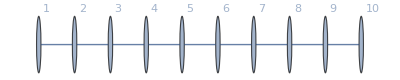

```mathematica
P=PathGraph[{1,2,3,4,5,6,7,8,9,10},VertexLabels->"Name"]
```

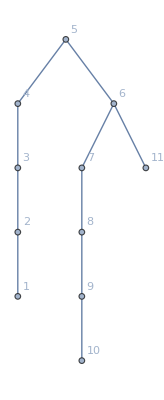

```mathematica
G=EdgeAdd[P,6<->11]
```

```mathematica
G
```

-Graphics-

```mathematica
Smash[G,{1}]
```

{{-(-3 L+17 L^3-20 L^5+8 L^7-L^9)/(-1+11 L^2-31 L^4+27 L^6-9 L^8+L^10)}}

```mathematica
Smash[G,{10}]
```

{{-(-4 L+17 L^3-20 L^5+8 L^7-L^9)/(11 L^2-31 L^4+27 L^6-9 L^8+L^10)}}

```mathematica
M=Smash[G,{1,10}]
```

{{-(-8 L^2+14 L^4-7 L^6+L^8)/(-3 L+17 L^3-20 L^5+8 L^7-L^9),-L/(-3 L+17 L^3-20 L^5+8 L^7-L^9)},{-L/(-3 L+17 L^3-20 L^5+8 L^7-L^9),-(1-8 L^2+14 L^4-7 L^6+L^8)/(-3 L+17 L^3-20 L^5+8 L^7-L^9)}}

```mathematica
f=M[[1,1]]-M[[2,2]]
```

-(-8 L^2+14 L^4-7 L^6+L^8)/(-3 L+17 L^3-20 L^5+8 L^7-L^9)+(1-8 L^2+14 L^4-7 L^6+L^8)/(-3 L+17 L^3-20 L^5+8 L^7-L^9)

```mathematica
Simplify[-(-8 L^2+14 L^4-7 L^6+L^8)/(-3 L+17 L^3-20 L^5+8 L^7-L^9)+(1-8 L^2+14 L^4-7 L^6+L^8)/(-3 L+17 L^3-20 L^5+8 L^7-L^9)]
```

-1/(3 L-17 L^3+20 L^5-8 L^7+L^9)

```mathematica
f
```

-(-8 L^2+14 L^4-7 L^6+L^8)/(-3 L+17 L^3-20 L^5+8 L^7-L^9)+(1-8 L^2+14 L^4-7 L^6+L^8)/(-3 L+17 L^3-20 L^5+8 L^7-L^9)

```mathematica
Simplify[-(-8 L^2+14 L^4-7 L^6+L^8)/(-3 L+17 L^3-20 L^5+8 L^7-L^9)+(1-8 L^2+14 L^4-7 L^6+L^8)/(-3 L+17 L^3-20 L^5+8 L^7-L^9)]
```

-1/(3 L-17 L^3+20 L^5-8 L^7+L^9)

```mathematica
Integrate[-1/(3 L-17 L^3+20 L^5-8 L^7+L^9),{L,0,Infinity}]
```

Integrate::idiv: Integral of -1/(3 L-17 L^3+20 L^5-8 L^7+L^9) does not converge on {0,∞}.

∫_0^∞ -1/(3 L-17 L^3+20 L^5-8 L^7+L^9)ⅆL

```mathematica
FullSimplify[Smash[G,{1}]-Smash[G,{10}]]
```

{{-((-2+L^2) (2-13 L^2+19 L^4-8 L^6+L^8))/(L (11-31 L^2+27 L^4-9 L^6+L^8) (-1+11 L^2-31 L^4+27 L^6-9 L^8+L^10))}}

```mathematica
Expand[-((-2+L^2) (2-13 L^2+19 L^4-8 L^6+L^8))/(L (11-31 L^2+27 L^4-9 L^6+L^8) (-1+11 L^2-31 L^4+27 L^6-9 L^8+L^10))]
```

4/(L (11-31 L^2+27 L^4-9 L^6+L^8) (-1+11 L^2-31 L^4+27 L^6-9 L^8+L^10))-(28 L)/((11-31 L^2+27 L^4-9 L^6+L^8) (-1+11 L^2-31 L^4+27 L^6-9 L^8+L^10))+(51 L^3)/((11-31 L^2+27 L^4-9 L^6+L^8) (-1+11 L^2-31 L^4+27 L^6-9 L^8+L^10))-(35 L^5)/((11-31 L^2+27 L^4-9 L^6+L^8) (-1+11 L^2-31 L^4+27 L^6-9 L^8+L^10))+(10 L^7)/((11-31 L^2+27 L^4-9 L^6+L^8) (-1+11 L^2-31 L^4+27 L^6-9 L^8+L^10))-L^9/((11-31 L^2+27 L^4-9 L^6+L^8) (-1+11 L^2-31 L^4+27 L^6-9 L^8+L^10))

```mathematica
Apart[%]
```

-4/(11 L)+(-1+L)/(4 (-1-L+L^2))+(1+L)/(4 (-1+L+L^2))+(4 L-5 L^3+L^5)/(2 (-1+8 L^2-6 L^4+L^6))+(63 L-112 L^3+52 L^5-7 L^7)/(11 (11-31 L^2+27 L^4-9 L^6+L^8))

```mathematica
Apart[-((-2+L^2) (2-13 L^2+19 L^4-8 L^6+L^8))/(L (11-31 L^2+27 L^4-9 L^6+L^8) (-1+11 L^2-31 L^4+27 L^6-9 L^8+L^10)),L]
```

-4/(11 L)+(-1+L)/(4 (-1-L+L^2))+(1+L)/(4 (-1+L+L^2))+(4 L-5 L^3+L^5)/(2 (-1+8 L^2-6 L^4+L^6))+(63 L-112 L^3+52 L^5-7 L^7)/(11 (11-31 L^2+27 L^4-9 L^6+L^8))

```mathematica
Simplify[-4/(11 L)+(-1+L)/(4 (-1-L+L^2))+(1+L)/(4 (-1+L+L^2))+(4 L-5 L^3+L^5)/(2 (-1+8 L^2-6 L^4+L^6))+(63 L-112 L^3+52 L^5-7 L^7)/(11 (11-31 L^2+27 L^4-9 L^6+L^8))]
```

(4-28 L^2+51 L^4-35 L^6+10 L^8-L^10)/(L (-1-L+L^2) (-1+L+L^2) (-1+8 L^2-6 L^4+L^6) (11-31 L^2+27 L^4-9 L^6+L^8))

```mathematica
Smash[P,{3,6}]
```

{{(2 L)/(-1+L^2),1/(-1+L^2)},{1/(-1+L^2),L/(-1+L^2)-(-1+L^2)/(2 L-L^3)}}

```mathematica
Simplify[%]
```

{{(2 L)/(-1+L^2),1/(-1+L^2)},{1/(-1+L^2),(1-4 L^2+2 L^4)/(2 L-3 L^3+L^5)}}

```mathematica
Smash[P,{3}]
```

{{L/(-1+L^2)-(-3 L+4 L^3-L^5)/(-1+6 L^2-5 L^4+L^6)}}

```mathematica
Simplify[%]
```

{{(L (-4+13 L^2-10 L^4+2 L^6))/(1-7 L^2+11 L^4-6 L^6+L^8)}}

```mathematica
Smash[P,{6}]
```

{{-(-1+L^2)/(2 L-L^3)-(1-3 L^2+L^4)/(-3 L+4 L^3-L^5)}}

```mathematica
Simplify[%]
```

{{(5-14 L^2+10 L^4-2 L^6)/(6 L-11 L^3+6 L^5-L^7)}}

```mathematica
Cfunct[G0_,S0_]:=Module[{G=G0,S=S0},n=Length[VertexList[G]];A=MyAdjacencyMatrix[G]; For[x=1,x≤Length[S],x++,G=EdgeAdd[G,{S[[x]]<->n+1}]];Simplify[CharacteristicPolynomial[A,L]*Smash[G,{n+1}][[1,1]]]]
```

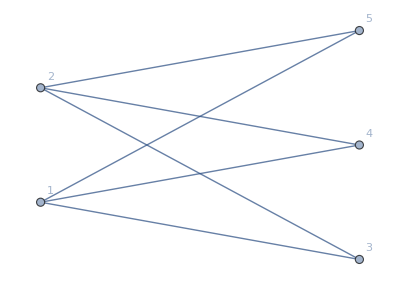

```mathematica
G=CompleteGraph[{2,3},VertexLabels->"Name"]
```

```mathematica
S={1,2}
```

{1,2}

```mathematica
Smash[G,S]
```

{{3/L,3/L},{3/L,3/L}}

```mathematica
Eigenvalues[{{3/L,3/L},{3/L,3/L}}]
```

```mathematica
({6/L,0}
(2-(4+72)^(1/2)))/(6)^(1/2)
```

{(√6 (2-2 √19))/L,0}

```mathematica
Eigenvalues[{{2/L,2/L,1},{2/L,2/L,1},{1,1,0}}]
```

```mathematica
{0,(2-√2 √(2+L^2))/L,(2+√2 √(2+L^2))/L}
Eigenvalues[MyAdjacencyMatrix[G]]
```

{0,(2-√2 √(2+L^2))/L,(2+√2 √(2+L^2))/L}

{-√6,√6,0,0,0}

```mathematica
(2-(4+2 L^2)^(1/2))/L
```

```mathematica
(2-√(4+2 L^2))/L=0
```

Set::write: Tag Times in (2-√(4+2 L^2))/L is Protected.

0

```mathematica
MatrixForm[{{1/L,1/L,1,1},{1/L,1/L,1,1},{1,1,0,0},{1,1,0,0}}]
```

(1/L | 1/L | 1 | 1
1/L | 1/L | 1 | 1
1 | 1 | 0 | 0
1 | 1 | 0 | 0)

```mathematica
Cfunct[G,S]
```

(6 L^3-L^5) (-(6 L^2)/(6 L^3-L^5)-(2 (-3 L^2+L^4))/(6 L^3-L^5))

```mathematica
Simplify[(6 L^3-L^5) (-(6 L^2)/(6 L^3-L^5)-(2 (-3 L^2+L^4))/(6 L^3-L^5))]
```

-2 L^4

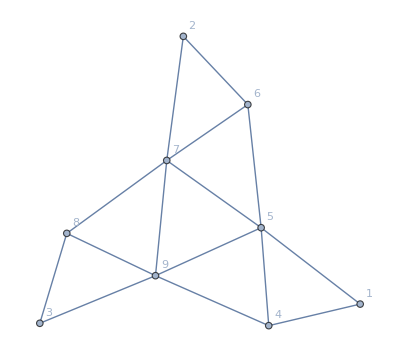

```mathematica
G=Graph[{1<->4,1<->5,2<->6,2<->7,3<->8,3<->9,4<->5,4<->9,5<->6,5<->7,5<->9,6<->7,7<->8,7<->9,8<->9},VertexLabels->"Name"]
```

```mathematica
MyAdjacencyMatrix[G]
```

{{0,0,0,1,1,0,0,0,0},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,1},{1,0,0,0,1,0,0,0,1},{1,0,0,1,0,1,1,0,1},{0,1,0,0,1,0,1,0,0},{0,1,0,0,1,1,0,1,1},{0,0,1,0,0,0,1,0,1},{0,0,1,1,1,0,1,1,0}}

```mathematica
Cfunct[G,{1,2,3}]
```

(8+48 L+90 L^2+30 L^3-72 L^4-51 L^5+14 L^6+15 L^7-L^9) (-(6 (-4-14 L-14 L^2+6 L^4+2 L^5))/(8+48 L+90 L^2+30 L^3-72 L^4-51 L^5+14 L^6+15 L^7-L^9)-(3 (-8-28 L-12 L^2+42 L^3+33 L^4-12 L^5-13 L^6+L^8))/(8+48 L+90 L^2+30 L^3-72 L^4-51 L^5+14 L^6+15 L^7-L^9))

```mathematica
Simplify[%13]
```

-3 (-4-2 L+L^2) (-2-3 L+L^2+L^3)^2

```mathematica
Expand[-3 (-4-2 L+L^2) (-2-3 L+L^2+L^3)^2]
```

48+168 L+120 L^2-126 L^3-135 L^4+24 L^5+39 L^6-3 L^8

```mathematica
Cfunct[G,{5,7,9}]
```

(8+48 L+90 L^2+30 L^3-72 L^4-51 L^5+14 L^6+15 L^7-L^9) (-(6 (2 L+5 L^2-7 L^4-3 L^5+2 L^6+L^7))/(8+48 L+90 L^2+30 L^3-72 L^4-51 L^5+14 L^6+15 L^7-L^9)-(3 (-4-16 L-11 L^2+22 L^3+24 L^4-6 L^5-10 L^6+L^8))/(8+48 L+90 L^2+30 L^3-72 L^4-51 L^5+14 L^6+15 L^7-L^9))

```mathematica
Simplify[%16]
```

-3 (-1+L^2) (-2-3 L+L^2+L^3)^2

```mathematica
Expand[-3 (-1+L^2) (-2-3 L+L^2+L^3)^2]
```

12+36 L+3 L^2-66 L^3-30 L^4+36 L^5+18 L^6-6 L^7-3 L^8

```mathematica
Cfunct[G,{5,7,9}]
```

-3 (-1+L^2) (-2-3 L+L^2+L^3)^2

```mathematica
Expand[-3 (-1+L^2) (-2-3 L+L^2+L^3)^2]
```

12+36 L+3 L^2-66 L^3-30 L^4+36 L^5+18 L^6-6 L^7-3 L^8

```mathematica
Cfunct[G,{3,4,5}]
```

-3 L^4

```mathematica
Cfunct[G,{1}]
```

-L^2 (-3+L^2)

```mathematica
Expand[-L^2 (-3+L^2)]
```

3 L^2-L^4

```mathematica
Cfunct[G,{3}]
```

-L^2 (-4+L^2)

```mathematica
Expand[-L^2 (-4+L^2)]
```

4 L^2-L^4

```mathematica
Smash[G,{1}]
```

{{(6 L)/(-3 L^2+L^4)-(3 (2 L-L^3))/(-3 L^2+L^4)}}

```mathematica
Flatten[{{(6 L)/(-3 L^2+L^4)-(3 (2 L-L^3))/(-3 L^2+L^4)}}]
```

{(6 L)/(-3 L^2+L^4)-(3 (2 L-L^3))/(-3 L^2+L^4)}

```mathematica
Simplify[%]
```

{(3 L)/(-3+L^2)}

```mathematica
CharacteristicPolynomial[MyAdjacencyMatrix[G],L]
```

6 L^3-L^5

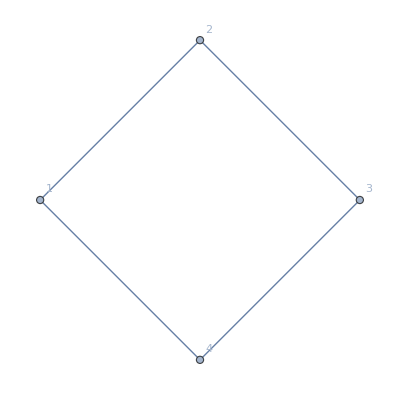

{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}}

```mathematica
G=Graph[{1<->2,2<->3,3<->4,4<->1},VertexLabels->"Name"]
MyAdjacencyMatrix[G]
```

```mathematica
{{1,2},{2,3},{3,4},{4,1}}
```

{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}}

```mathematica
Eigenvalues[{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}}]
```

{-2,2,0,0}

```mathematica
A = MyAdjacencyMatrix[G]
```

{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}}

```mathematica
Smash[G,{1,2,3}]
```

Smash[-Graphics-,{1,2,3}]

```mathematica
B={{-0.5,1,-0.5},{1,0,1},{-0.5,1,-0.5}}
```

{{-0.5,1,-0.5},{1,0,1},{-0.5,1,-0.5}}

```mathematica
Eigenvalues[B]
```

{-2.,1.,1.21431×10^-16}